# POZOR

Shranjevat, operacije z regionsi pogosto kreširajo Mathematico.

# OSNOVNI

parametrični

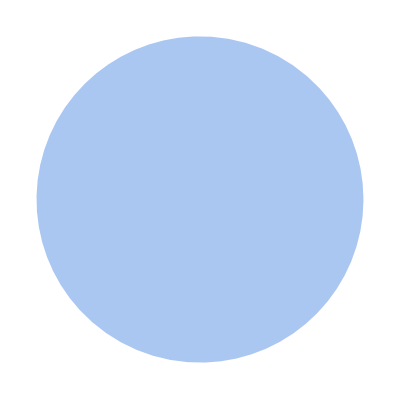

```mathematica
Region@ParametricRegion[{r Cos[θ],r Sin[θ]},{{θ,0,2 π},{r,0,1}}]
```

implicitni

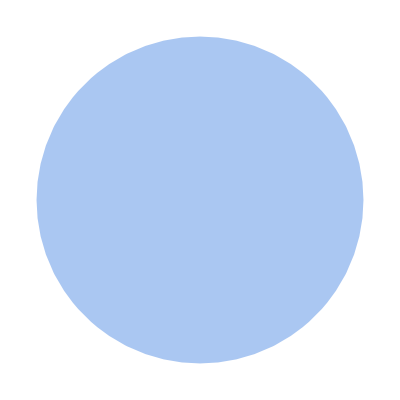

```mathematica
Region@ImplicitRegion[x^2+y^2<=1,{x,y}]
```

mesh

```mathematica
MeshRegion[
	{{0,0,0},{1,0,0},{0,1,0},{0,0,1},  .5{1,1,0},{1,1,0},{1,1,1},    {1,0,1}},
	{
		Polyhedron@{{3,2,1},{1,2,4},{1,4,3},{2,3,4}},
		Polygon@{4,5,6,7},
		Line@{7,2,6,3,7},
		Point@8
	}
]
```

-Graphics3D-

Enostavne oblike, kot stožec, valj, ...: To bo pri OSTALE GRAFIKE

Sicer pa z  MeshRegion itak lahko sestaviš karkoli

# ŠE NEKAJ O MESHIH

## IZ SEZNAMA PLOSKEV

Tko dobiš oglišča in indekse:

```mathematica
PloskveVOglInd[Ploskve_]:=(
	OAssI=Association[];
	ind=0;
	indjiji=Map[
		If[KeyExistsQ[OAssI,#],
			OAssI[#],
			ind++; OAssI[#]=ind; ind 
		]&, Ploskve, {2}
	];
	{Keys@OAssI,indjiji}
);

PloskveVOglInd@{
	{{0,0,0},{1,0,0},{1,1,0},{0,1,0}},
	{{0,0,0},{1,0,0},{.5,.5,1}},
	{{1,0,0},{1,1,0},{.5,.5,1}},
	{{1,1,0},{0,1,0},{.5,.5,1}},
	{{0,1,0},{0,0,0},{.5,.5,1}}
}
```

{{{0,0,0},{1,0,0},{1,1,0},{0,1,0},{0.5,0.5,1}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{4,1,5}}}

```mathematica
MeshRegion[%[[1]],Polyhedron@%[[2]]]
```

-Graphics3D-

Za nazaj v seznam ploskev pa:

```mathematica
{ogljiji,indjiji}=%%;
ParallelMap[ogljiji[[#]]&,indjiji,{2}]
```

{{{0,0,0},{1,0,0},{1,1,0},{0,1,0}},{{0,0,0},{1,0,0},{0.5,0.5,1}},{{1,0,0},{1,1,0},{0.5,0.5,1}},{{1,1,0},{0,1,0},{0.5,0.5,1}},{{0,1,0},{0,0,0},{0.5,0.5,1}}}

## KONVEKSNA OGRINJAČA

```mathematica
KonvOgr=ConvexHullMesh@RandomReal[1,{100,3}]
```

-Graphics3D-

```mathematica
MeshCoordinates@KonvOgr
MeshCells[KonvOgr,2]/.Polygon[o_]->o    (*2 stoji za 2D ploskve*)
```

{{0.352546,0.0174168,0.733431},{0.956563,0.565401,0.289404},{0.925196,0.269206,0.887458},{0.367532,0.392828,0.955005},{0.0417712,0.00832371,0.296073},{0.966518,0.0712339,0.324468},{0.800868,0.812069,0.238895},{0.821641,0.504151,0.998414},{0.637712,0.926865,0.791336},{0.897792,0.570481,0.0233785},{0.14838,0.018233,0.896168},{0.0466183,0.112379,0.928108},{0.23897,0.679585,0.0338639},{0.668208,0.794971,0.130733},{0.00274483,0.656759,0.810246},{0.962835,0.865107,0.929512},{0.678961,0.112742,0.85187},{0.703889,0.753433,0.948168},{0.473288,0.564281,0.959953},{0.379107,0.108549,0.0568243},{0.551382,0.635598,0.0258467},{0.154424,0.830919,0.861691},{0.676302,0.89111,0.92292},{0.759994,0.0191306,0.0944846},{0.924505,0.996906,0.603646},{0.36895,0.889507,0.169627},{0.823496,0.189045,0.0145664},{0.00473265,0.112206,0.194896},{0.21201,0.0116436,0.825366},{0.314857,0.3978,0.0417591},{0.0345612,0.93846,0.187764},{0.43015,0.0835604,0.967052},{0.378689,0.90596,0.781627}}

{{23,16,25},{16,23,8},{3,16,8},{16,3,6},{31,33,25},{10,2,6},{2,16,6},{2,10,25},{16,2,25},{26,31,25},{31,26,13},{19,4,8},{3,17,6},{32,3,8},{32,17,3},{17,1,6},{32,1,17},{12,5,11},{19,12,4},{32,12,11},{4,12,8},{12,32,8},{9,23,25},{33,9,25},{9,33,23},{33,22,23},{22,33,31},{22,19,23},{22,31,15},{12,22,15},{22,12,19},{10,7,25},{26,21,13},{23,18,8},{18,19,8},{19,18,23},{5,29,11},{29,32,11},{29,1,32},{27,10,6},{27,21,10},{21,27,13},{28,20,5},{28,31,13},{31,28,15},{28,12,15},{12,28,5},{21,14,10},{14,21,26},{14,7,10},{14,26,25},{7,14,25},{27,30,13},{30,27,20},{30,28,13},{28,30,20},{27,24,20},{20,24,5},{24,27,6},{1,24,6},{24,29,5},{29,24,1}}

```mathematica
MeshRegion[%%,Polyhedron@%]
```

-Graphics3D-

# SESTAVLJANJE

```mathematica
RegionUnion[-Graphics3D-, -Graphics3D-]
```

-Graphics3D-


```mathematica
RegionIntersection[-Graphics-,-Graphics-]
```

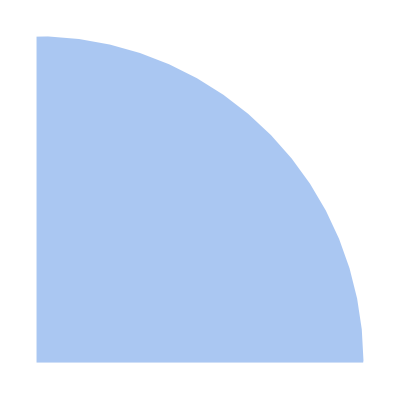

```mathematica
RegionIntersection[-Graphics3D-, -Graphics3D-]
```

-Graphics3D-

```mathematica
reg=RegionDifference[-Graphics3D-, -Graphics3D-]
```

-Graphics3D-

# PAR STVARI, KI JIH ZA REGIONSE LAH ZRAČUNAMO

```mathematica
Volume@reg
SurfaceArea@reg
MomentOfInertia@reg
RegionCentroid@reg
NIntegrate[x^2 y^2 + Sin[x+z], {x, y, z} ∈ reg]
```

0.90356

6.50292

{{0.14728,1.57628×10^-12,7.68796×10^-14},{1.57628×10^-12,0.160226,0.000345782},{7.68796×10^-14,0.000345782,0.148951}}

{0.5,0.539454,0.502463}

0.806792

# DRUGO

```mathematica
Glej Tudi:
```

https://www.youtube.com/watch?v=X-3LKVfvEqc&ab_channel=Wolfram

https://reference.wolfram.com/language/guide/GeometricComputation.html

https://reference.wolfram.com/language/guide/DerivedRegions.html